# Neural Logic Networks

## A classification problem

This is a demo of a new kind of neural network architecture.
To explain what it is, and why it’s useful, we need to compare it to a standard neural network.
So let’s begin with a machine learning problem.

```mathematica
data=ResourceData["663653b1-6151-48ad-b693-3ee813b191c6"]
```

Dataset[<>]

This describes various features of cars -- such as their price, maintenance cost, number of doors and so on. 
The goal is to predict whether a particular car is an acceptable purchase. 
In other words, we want to predict the last column of this table from the first 6 columns.
Let’s begin by splitting this data into a training and test set.

```mathematica
{trainData,testData}=[data,"TestSetSize"->Scaled[0.1],"Shuffle"->True];
```

## Utilities

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

### Feature encoders

```mathematica
Encoders[data_]:=Block[{features=Normal[Keys@First[data]],featureValues},
featureValues={#,Normal[DeleteDuplicates[data[All,#]]]}&/@features;
Association[First[#]->NetEncoder[{"Class",Last[#],"IndicatorVector"}]&/@featureValues]
]
encoders=Encoders[trainData];
inputSize=Total[First[#["Output"]]&/@Normal/@Values[Drop[encoders,-1]]];
classes=Normal[DeleteDuplicates[data[All,"Acceptability"]]];
```

```mathematica
featureLayer=NetGraph[<|"Catenate"->CatenateLayer[]|>,
Map[NetPort[First[#]]->"Catenate"&,Drop[Normal[encoders],-1]],Sequence@@Normal[Drop[Normal[encoders],-1]]
];
```

### Define standard net

```mathematica
StandardNet[]:=Module[{standardNet,net},
standardNet=NetChain[{LinearLayer[20,"Input"->inputSize],ElementwiseLayer["ScaledExponentialLinearUnit"],LinearLayer[4],SoftmaxLayer[]}];
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->standardNet|>,{"FeatureLayer"->"SoftNet"}];
NetGraph[
<|"Net"->net,"Loss"->CrossEntropyLossLayer["Probabilities"]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
]
]
```

### Train standard net

```mathematica
TrainStandardNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
TrainingStoppingCriterion->Function[#ValidationLoss<0.02],
MaxTrainingRounds->Infinity,
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real32"];
```

```mathematica
GetTrainedStandardNet[result_]:=NetGraph[
<|"TrainedNet"->NetDelete[result["TrainedNet"],"Loss"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
]
```

### Evaluate standard net

```mathematica
EvaluateStandardNet[trainedStandardNet_,testData_]:=Module[{predictions,eval},
predictions=Association[{"Prediction"->trainedStandardNet[KeyDrop[{"Acceptability"}]@#],"Target"->#["Acceptability"]}]&/@Normal[testData];
eval=HardNetClassifyEvaluation[predictions];
{predictions,eval}
]
```

```mathematica
GetStandardWeights[trainedStandardNet_]:=Module[{},
Flatten[Normal/@DeleteMissing[Values[Quiet[NetExtract[NetFlatten[trainedStandardNet],{All,"Weights"}]]]]]
]
```

### Define neural logic net

```mathematica
NeuralLogicNet[]:=Module[{softNet,hardNet,net,trainableNet},
{softNet,hardNet}=HardNeuralChain[{
HardNeuralOR[inputSize,64],
HardNeuralNOT[64,Length[classes]]
}];
net=NetGraph[<|"FeatureLayer"->featureLayer,"SoftNet"->softNet|>,{"FeatureLayer"->"SoftNet"}];
trainableNet=NetGraph[
<|"Net"->net,"Loss"->HardClassificationLoss[]|>,
{NetPort["Acceptability"]->NetPort["Loss","Target"],"Net"->"Loss"},
"Acceptability"->encoders["Acceptability"]
];
{trainableNet,hardNet}
]
```

### Train neural logic net

```mathematica
TrainNeuralLogicNet[net_,trainData_,testData_]:=NetTrain[net,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
TrainingStoppingCriterion->Function[#ValidationLoss<0.02],
Method->{"ADAM"},
TargetDevice->"GPU",
WorkingPrecision->"Real64",
MaxTrainingRounds->Infinity]
```

```mathematica
GetTrainedNeuralLogicNet[result_]:=NetGraph[
<|"TrainedNet"->NetDelete[result["TrainedNet"],"Loss"]|>,
{}
]
```

### Evaluate neural logic net

```mathematica
EvaluateNeuralLogicNet[hardNetFunction_,testData_]:=Module[{predictions,eval},
predictions=HardNetClassify[hardNetFunction,testData,NetDecoder[encoders["Acceptability"]],featureLayer[KeyDrop[#,"Acceptability"]]&,#["Acceptability"]&];eval=HardNetClassifyEvaluation[predictions];
{predictions,eval}
]
```

```mathematica
GetNeuralLogicWeights[trainedNeuralLogicNet_]:=Harden[Flatten[ExtractWeights[trainedNeuralLogicNet]]]
```

## A standard neural network

Now we define a standard neural network that can learn this classification problem.

```mathematica
standardNet=StandardNet[]
```

NetGraph[<>]

This net takes car features as input, converts them to real-valued vectors, processes those inputs, and then predicts the car’s Acceptability.
We can flatten the net to get a closer look at its architecture.

```mathematica
NetFlatten[standardNet]
```

NetGraph[<>]

The net has 2 layers: a first layer of 20 nonlinear neurons, and a second layer of 4 linear neurons.
I chose this architecture because it’s the smallest network that can learn the classification problem.
The final output is a real-valued vector of size 4, which corresponds to the 4 possible values of Acceptability, which is “acceptable”, “unacceptable”, “good” and “very good”.
This vector is then converted to a probability distribution and the loss function is a standard cross-entropy loss.
We can therefore train the weights of this network from the data. So let’s do that.

```mathematica
result=TrainStandardNet[standardNet,trainData,testData]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:9475  rounds:379  time:28s  examples/s:22441
data | ,,  training examples:1555  validation examples:173  processed examples:606400  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.09×10^-2  error:0%
validation | ,,  loss:1.97×10^-2  error:0%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

I chose the car dataset because it’s quite small, and so I can demo in real-time.
We can see the loss on the training and validation set decreasing.
And we can see the predictive accuracy of the net increasing.
It takes about 30 seconds to get high accuracy on the validation set.
Once trained, we can extract the trained classifier.

```mathematica
trainedStandardNet=GetTrainedStandardNet[result]
```

NetGraph[<>]

Now we have a nonlinear function that can predict the acceptability of a car.
Let’s evaluate it on the test data.

```mathematica
{predictions,summary}=EvaluateStandardNet[trainedStandardNet,testData];
```

We can eyeball the predictions of the net compared to the ground truth.

```mathematica
predictions
```

And we can measure the overall accuracy of the net.

```mathematica
summary["Accuracy"]
```

1.

How big is the net? To find out we can extract the learned weights.

```mathematica
standardWeights=GetStandardWeights[trainedStandardNet];
```

Now each weight is typically either a 32-bit or 64-bit number. So the RAM cost of this particular classifier turns out to be about 16K.

```mathematica
standardNetSize=Quantity[Length[standardWeights]*32/1024.0,"Kilobytes"]
```

15.625 kB

This is a small dataset. 16K for a single classifier isn’t much memory. But for bigger problems the size of NNs can rapidly become very large.
For some applications, memory is a scarce. For example, in the ATM project we had to control the size of the NN that integrates with CodeQL to avoid OOM errors.
And we’ll want to integrate many more predictive models in the future.
So can we do better? Can we get the same predictive performance but for less memory cost?
Also, we have ideas for making learning a first-class citizen of the QL language. But to achieve that vision we’d need to back-propagate through non-differentiable logical predicates.
So, for all these reasons, we need a different kind of neural network, which for now I’m calling a “neural logic network”.

## A neural logic network

Let’s define a neural logic network that can learn the same “cars” problem as before.

```mathematica
{softNet,hardNet}=NeuralLogicNet[];
```

Notice that we’ve actually defined 2 things here: a soft net, and a hard net. Ignore the hard net for now.
Let’s flatten the soft net to examine the architecture.

```mathematica
NetFlatten[softNet]
```

NetGraph[<>]

As before, this net takes as input the 6 car features.
And, as before, the net outputs 4 probability values and uses a cross-entropy loss.
But otherwise the architecture is quite different.
In fact, this net also has 2 layers.
I chose this architecture because it’s the smallest neural-logic network that can learn the classification problem.
The first layer consists of 64 neurons that act like the logical OR operator but are continuous functions and therefore differentiable.
The second layer consists of 4 neurons that act like the logical NOT operator but are also differentiable.
The learnable real-valued weights in this net are real-valued “soft bits” that range between 0 and 1.
They control whether specific OR or NOT operations are active.
Although the semantics correspond to non-differentiable logical operations the entire net is end-to-end differentiable.
So we can train it like a normal neural network.
Let’s  do that.

```mathematica
result=TrainNeuralLogicNet[softNet,trainData,testData]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:15625  rounds:625  time:56s  examples/s:17945
data | ,,  training examples:1555  validation examples:173  processed examples:1000000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.21×10^-2  error:0.625%
validation | ,,  loss:1.83×10^-2  error:0%
 | 
-Graphics-  training set	-Graphics-  validation set | ]

It takes about a minute to get high accuracy on the validation set.
So training takes longer.
Neural-logic nets have the same worst-case time-complexity as standard nets but there is a constant cost to pay.
Also neural-logic nets require more memory at training time.
But the additional training costs yield the benefit of very compact classifiers that are cheap to query and have the same predictive performance, as we’re about to see.
Let’s extract the trained net.

```mathematica
trainedNeuralLogicNet=GetTrainedNeuralLogicNet[result];
```

Now, when we defined the neural-logic net we got 2 things: a soft net and a hard net.
These are 2 different representations of the same network architecture.
The soft net uses real weights, and is a differentiable nonlinear function.
The hard net uses boolean weights, and is a non-differentiable, discrete boolean function.

Now comes the trick!
We use the soft net to learn real-valued weights.
Then we convert the real-valued weights to boolean-valued weights, just True and False.
And then we use the boolean weights with the hard net.
Unlike existing binarization techniques this conversion is perfect ... we don’t introduce any approximation error.
Let’s do this now.

```mathematica
hnf=HardNetFunction[hardNet,trainedNeuralLogicNet];
hnbe=HardNetBooleanExpression[hnf,inputSize]
```

{{b6||b11||b14||b17||b19||b21,b1||b3||b6||b14||b20||b21,b1||b5,b2||b8||b10||b14||b16||b18||b20||b21,!(b2||b6||b10||b17||b20),!(b4||b6||b14||b21),b1||b3||b5||b7,!(b3||b4||b5||b6||b7||b14||b21),!(b4||b11||b14||b17||b21),b9||b11||b12||b13||b16,!(b1||b2||b5||b8||b14||b17||b21),!(b2||b4||b14||b17||b21),!(b9||b12||b15||b16||b17||b19),!(b2||b4||b8||b14||b17||b21),!(b6||b14||b17||b20||b21),!(b2||b4||b14||b21),b10||b14||b17||b19||b21,b1||b13||b18,!(b2||b6||b8||b14||b21),b1||b2||b5,!(b2||b4||b6||b14||b17||b18||b20),b2||b4||b6||b8||b16||b20,b9||b11||b12||b13||b14||b16,!(b9||b11||b12||b13||b16||b18),!(b2||b4||b6||b8||b10||b14||b17||b21),b1||b3||b6||b8||b14||b17||b21,!(b13||b15),!(b2||b4||b6||b8||b14||b20||b21),!(b4||b6||b14||b21),b2||b8||b14||b21,b8||b14||b17||b18||b19||b21,!(b8||b14||b20||b21),b1||b5||b7,!(b6||b14||b17||b21),b9||b11||b12||b13||b16,b2||b5||b7||b16||b19,b1||b4||b5||b14||b20||b21,!(b2||b4||b10||b11||b14||b17||b20||b21),!(b4||b10||b13||b14||b21),!(b2||b4||b6||b10||b14||b16||b17||b21),b6||b14||b21,b3||b4||b5||b8,b1||b3||b16,!(b2||b4||b6||b8||b14||b17||b18||b21),!(b2||b3||b6||b7||b20),b2||b4||b6||b8||b9||b12||b14||b15||b16||b20||b21,!(b2||b4||b6||b8||b14||b17||b21),b9||b12||b14||b15||b16||b20||b21,b9||b12||b15||b16||b17||b19,!(b2||b4||b6||b8||b10||b14||b21),!(b2||b4||b6||b8||b20),!(b6||b10||b13||b14||b16||b21),b14||b16||b20||b21,!(b13||b15),b9||b12||b16,!(b4||b5||b14||b21),b1||b5,b1||b16||b19,!(b2||b4||b6||b11||b14||b17||b21),!(b6||b14||b20||b21),b9||b12||b15||b16||b17||b19,!(b10||b14||b16||b20||b21),!(b2||b4||b6||b9||b12||b14||b17||b18||b21),!(b2||b4||b6||b14||b17||b20||b21)},{b6||b11||b14||b17||b19||b21,b1||b3||b6||b14||b20||b21,!(b1||b5),b2||b8||b10||b14||b16||b18||b20||b21,!(b2||b6||b10||b17||b20),b4||b6||b14||b21,!(b1||b3||b5||b7),b3||b4||b5||b6||b7||b14||b21,b4||b11||b14||b17||b21,!(b9||b11||b12||b13||b16),b1||b2||b5||b8||b14||b17||b21,b2||b4||b14||b17||b21,!(b9||b12||b15||b16||b17||b19),b2||b4||b8||b14||b17||b21,b6||b14||b17||b20||b21,b2||b4||b14||b21,b10||b14||b17||b19||b21,!(b1||b13||b18),b2||b6||b8||b14||b21,!(b1||b2||b5),b2||b4||b6||b14||b17||b18||b20,!(b2||b4||b6||b8||b16||b20),!(b9||b11||b12||b13||b14||b16),!(b9||b11||b12||b13||b16||b18),b2||b4||b6||b8||b10||b14||b17||b21,b1||b3||b6||b8||b14||b17||b21,!(b13||b15),b2||b4||b6||b8||b14||b20||b21,b4||b6||b14||b21,b2||b8||b14||b21,b8||b14||b17||b18||b19||b21,b8||b14||b20||b21,!(b1||b5||b7),b6||b14||b17||b21,!(b9||b11||b12||b13||b16),!(b2||b5||b7||b16||b19),b1||b4||b5||b14||b20||b21,b2||b4||b10||b11||b14||b17||b20||b21,b4||b10||b13||b14||b21,b2||b4||b6||b10||b14||b16||b17||b21,b6||b14||b21,!(b3||b4||b5||b8),!(b1||b3||b16),b2||b4||b6||b8||b14||b17||b18||b21,!(b2||b3||b6||b7||b20),b2||b4||b6||b8||b9||b12||b14||b15||b16||b20||b21,b2||b4||b6||b8||b14||b17||b21,b9||b12||b14||b15||b16||b20||b21,!(b9||b12||b15||b16||b17||b19),b2||b4||b6||b8||b10||b14||b21,!(b2||b4||b6||b8||b20),b6||b10||b13||b14||b16||b21,b14||b16||b20||b21,!(b13||b15),!(b9||b12||b16),b4||b5||b14||b21,!(b1||b5),!(b1||b16||b19),b2||b4||b6||b11||b14||b17||b21,b6||b14||b20||b21,!(b9||b12||b15||b16||b17||b19),b10||b14||b16||b20||b21,b2||b4||b6||b9||b12||b14||b17||b18||b21,b2||b4||b6||b14||b17||b20||b21},{!(b6||b11||b14||b17||b19||b21),!(b1||b3||b6||b14||b20||b21),b1||b5,!(b2||b8||b10||b14||b16||b18||b20||b21),b2||b6||b10||b17||b20,!(b4||b6||b14||b21),b1||b3||b5||b7,!(b3||b4||b5||b6||b7||b14||b21),!(b4||b11||b14||b17||b21),b9||b11||b12||b13||b16,!(b1||b2||b5||b8||b14||b17||b21),!(b2||b4||b14||b17||b21),b9||b12||b15||b16||b17||b19,!(b2||b4||b8||b14||b17||b21),!(b6||b14||b17||b20||b21),!(b2||b4||b14||b21),!(b10||b14||b17||b19||b21),b1||b13||b18,!(b2||b6||b8||b14||b21),!(b1||b2||b5),b2||b4||b6||b14||b17||b18||b20,b2||b4||b6||b8||b16||b20,b9||b11||b12||b13||b14||b16,b9||b11||b12||b13||b16||b18,b2||b4||b6||b8||b10||b14||b17||b21,!(b1||b3||b6||b8||b14||b17||b21),b13||b15,b2||b4||b6||b8||b14||b20||b21,!(b4||b6||b14||b21),!(b2||b8||b14||b21),!(b8||b14||b17||b18||b19||b21),!(b8||b14||b20||b21),b1||b5||b7,!(b6||b14||b17||b21),b9||b11||b12||b13||b16,b2||b5||b7||b16||b19,!(b1||b4||b5||b14||b20||b21),!(b2||b4||b10||b11||b14||b17||b20||b21),!(b4||b10||b13||b14||b21),b2||b4||b6||b10||b14||b16||b17||b21,!(b6||b14||b21),b3||b4||b5||b8,b1||b3||b16,b2||b4||b6||b8||b14||b17||b18||b21,b2||b3||b6||b7||b20,b2||b4||b6||b8||b9||b12||b14||b15||b16||b20||b21,b2||b4||b6||b8||b14||b17||b21,!(b9||b12||b14||b15||b16||b20||b21),b9||b12||b15||b16||b17||b19,b2||b4||b6||b8||b10||b14||b21,b2||b4||b6||b8||b20,b6||b10||b13||b14||b16||b21,!(b14||b16||b20||b21),b13||b15,b9||b12||b16,!(b4||b5||b14||b21),!(b1||b5),b1||b16||b19,b2||b4||b6||b11||b14||b17||b21,b6||b14||b20||b21,b9||b12||b15||b16||b17||b19,!(b10||b14||b16||b20||b21),b2||b4||b6||b9||b12||b14||b17||b18||b21,b2||b4||b6||b14||b17||b20||b21},{!(b6||b11||b14||b17||b19||b21),b1||b3||b6||b14||b20||b21,b1||b5,!(b2||b8||b10||b14||b16||b18||b20||b21),b2||b6||b10||b17||b20,!(b4||b6||b14||b21),b1||b3||b5||b7,b3||b4||b5||b6||b7||b14||b21,!(b4||b11||b14||b17||b21),b9||b11||b12||b13||b16,b1||b2||b5||b8||b14||b17||b21,!(b2||b4||b14||b17||b21),b9||b12||b15||b16||b17||b19,!(b2||b4||b8||b14||b17||b21),b6||b14||b17||b20||b21,!(b2||b4||b14||b21),!(b10||b14||b17||b19||b21),b1||b13||b18,!(b2||b6||b8||b14||b21),b1||b2||b5,b2||b4||b6||b14||b17||b18||b20,!(b2||b4||b6||b8||b16||b20),b9||b11||b12||b13||b14||b16,b9||b11||b12||b13||b16||b18,!(b2||b4||b6||b8||b10||b14||b17||b21),!(b1||b3||b6||b8||b14||b17||b21),!(b13||b15),!(b2||b4||b6||b8||b14||b20||b21),!(b4||b6||b14||b21),!(b2||b8||b14||b21),!(b8||b14||b17||b18||b19||b21),!(b8||b14||b20||b21),!(b1||b5||b7),!(b6||b14||b17||b21),b9||b11||b12||b13||b16,b2||b5||b7||b16||b19,b1||b4||b5||b14||b20||b21,b2||b4||b10||b11||b14||b17||b20||b21,!(b4||b10||b13||b14||b21),!(b2||b4||b6||b10||b14||b16||b17||b21),!(b6||b14||b21),!(b3||b4||b5||b8),b1||b3||b16,!(b2||b4||b6||b8||b14||b17||b18||b21),!(b2||b3||b6||b7||b20),!(b2||b4||b6||b8||b9||b12||b14||b15||b16||b20||b21),!(b2||b4||b6||b8||b14||b17||b21),!(b9||b12||b14||b15||b16||b20||b21),b9||b12||b15||b16||b17||b19,!(b2||b4||b6||b8||b10||b14||b21),!(b2||b4||b6||b8||b20),!(b6||b10||b13||b14||b16||b21),!(b14||b16||b20||b21),b13||b15,b9||b12||b16,b4||b5||b14||b21,b1||b5,b1||b16||b19,!(b2||b4||b6||b11||b14||b17||b21),!(b6||b14||b20||b21),b9||b12||b15||b16||b17||b19,b10||b14||b16||b20||b21,!(b2||b4||b6||b9||b12||b14||b17||b18||b21),b2||b4||b6||b14||b17||b20||b21}}

This expression is a Boolean function. Each b, from 1 to 21, is a single input bit, which together represent a car’s features.

```mathematica
Harden[Normal[featureLayer[Drop[testData[[1]],-1]]]]
```

{False,False,False,True,False,True,False,False,True,False,False,False,False,False,True,True,False,False,False,False,True}

The output is a vector of boolean values which can be interpreted as a probability distribution.
Notice that the boolean function is a combination of NOTs and ORs, which corresponds to the architecture of the neural-logic net.

```mathematica
hnf[%]
```

{{True,True,False,True,False,False,False,False,False,True,False,False,False,False,False,False,True,False,False,False,False,True,True,False,False,True,False,False,False,True,True,False,False,False,True,True,True,False,False,False,True,True,True,False,False,True,False,True,True,False,False,False,True,False,True,False,False,True,False,False,True,False,False,False},{True,True,True,True,False,True,True,True,True,False,True,True,False,True,True,True,True,True,True,True,True,False,False,False,True,True,False,True,True,True,True,True,True,True,False,False,True,True,True,True,True,False,False,True,False,True,True,True,False,True,False,True,True,False,False,True,True,False,True,True,False,True,True,True},{False,False,False,False,True,False,False,False,False,True,False,False,True,False,False,False,False,False,False,True,True,True,True,True,True,False,True,True,False,False,False,False,False,False,True,True,False,False,False,True,False,True,True,True,True,True,True,False,True,True,True,True,False,True,True,False,True,True,True,True,True,False,True,True},{False,True,False,False,True,False,False,True,False,True,True,False,True,False,True,False,False,False,False,False,True,False,True,True,False,False,False,False,False,False,False,False,True,False,True,True,True,True,False,False,False,False,True,False,False,False,False,False,True,False,False,False,False,True,True,True,False,True,False,False,True,True,False,True}}

Let’s evaluate this learned boolean function on the test data.

```mathematica
{predictions,summary}=EvaluateNeuralLogicNet[hnf,testData];
```

```mathematica
summary["Accuracy"]
```

1.

What do the weights look like?

```mathematica
neuralLogicWeights=GetNeuralLogicWeights[result["TrainedNet"]];
```

So the weights can be compactly represented as bit vectors. Each weight costs 1 bit. So the total size of this classifier is very small.

```mathematica
neuralLogicNetSize=Quantity[Length[neuralLogicWeights]/8/1024//N,"Kilobytes"]
```

0.195313 kB

```mathematica
standardNetSize/neuralLogicNetSize
```

80.

In fact, in this case the neural-logic classifier is 80 times smaller than standard net on the same problem. That’s a lot smaller.
And evaluating a boolean function can be a lot cheaper than evaluating a nonlinear real-valued function.
Different kinds of machine learning problems will generate different kinds of savings.
But neural-logic nets are always going to be smaller.
And we build boolean function analogues of all the existing kinds of neural network architectures.
And this kind of network is just the kind of thing we need to integrate NN learning with QL at a fundamental level.
That’s it for now!
Want to find out more? Visit the repo: https://github.com/github/neural-logic

```mathematica
diagram=Import["/home/wright/Downloads/neural-logic-net.png"]
```

-Graphics-

## Notes

```mathematica
{trainedSoftNet,trainedHardNet}=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[#],"Loss/Error"]|>,
{},"Output"->NetDecoder[encoders["Acceptability"]]
]&/@{result["TrainedNet"],HardenNet[result["TrainedNet"]]};
```

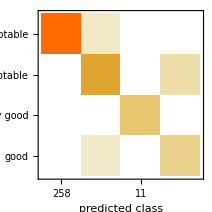
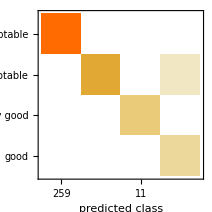
{Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (98.80.6) %
Accuracy baseline | (74.92.3) %
Geometric mean of probabilities | 0.973 ± 0.013
Mean cross entropy | 0.0273 ± 0.014
Single evaluation time | 6.86 ms/example
Batch evaluation speed | 1.34 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 346
Accuracy | (99.40.4) %
Accuracy baseline | (74.92.3) %
Geometric mean of probabilities | 0.974 ± 0.014
Mean cross entropy | 0.026 ± 0.015
Single evaluation time | 7.02 ms/example
Batch evaluation speed | 1.08 examples/ms
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData->"Acceptability"]&/@{trainedSoftNet,trainedHardNet}
```

```mathematica
hncwt2=Association[{"Prediction"->trainedHardNet[KeyDrop[{"Acceptability"}]@#],"Target"->#["Acceptability"]}]&/@Normal[testData];
eval2=HardNetClassifyEvaluation[hncwt2];
eval2["Accuracy"]
```

0.99422